# 3.2 Stability exponents for a toy model

### a)

```mathematica
(*creating the dynamical system and determine r0*)
rDot[r_,μ_]:=μ*r-r^3;
θDot [r_,μ_,ω_,ν_]:=ω+ν*r^2;
rSols = Solve[rDot[r,μ]==0,r];
r0 = r/.rSols[[3]]
```

√μ

```mathematica
(*calculating the velocity and also the circumference of circle to get the period time*)
velocity = r0*θDot[r0,μ,ω,ν];
distance = 2*Pi*r0;
periodT = distance/velocity
```

(2 π)/(μ ν+ω)

### b)

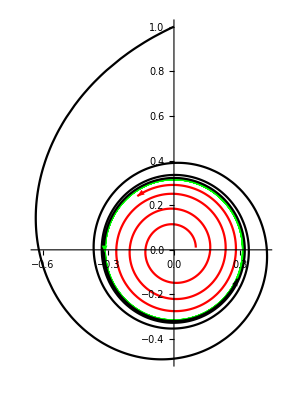

```mathematica
(*Dynamical system 2*)
X1Dot[X1_,X2_]:=1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2Dot[X1_,X2_]:=X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;

F[{X1_,X2_}]:={X1Dot[X1,X2],X2Dot[X1,X2]};




limitCycle=NDSolve[{X1'[t]==F[{X1[t],X2[t]}][[1]],X2'[t]==F[{X1[t],X2[t]}][[2]],X1[0]==Sqrt[1/10],X2[0]==0.01},{X1,X2},{t,0,20}];
outside=NDSolve[{X1'[t]==F[{X1[t],X2[t]}][[1]],X2'[t]==F[{X1[t],X2[t]}][[2]],X1[0]==0.1,X2[0]==0.01},{X1,X2},{t,0,20}];
inside=NDSolve[{X1'[t]==F[{X1[t],X2[t]}][[1]],X2'[t]==F[{X1[t],X2[t]}][[2]],X1[0]==0,X2[0]==1},{X1,X2},{t,0,20}];

p1 = ParametricPlot[Evaluate[{X1[t],X2[t]}/. limitCycle],{t,0,20},PlotStyle->Green]/.Line[x_]->{Arrowheads[{{0.05,0.1},{0.05,0.4},{0.05,0.6},{0.05,0.7}}],Arrow[x]};
p2 = ParametricPlot[Evaluate[{X1[t],X2[t]}/. outside],{t,0,20},PlotStyle->Red]/.Line[x_]->{Arrowheads[{{0.05,0.1},{0.05,0.4},{0.05,0.6},{0.05,0.7}}],Arrow[x]};
p3 = ParametricPlot[Evaluate[{X1[t],X2[t]}/. inside],{t,0,20},PlotStyle->Black]/.Line[x_]->{Arrowheads[{{0.05,0.1},{0.05,0.4},{0.05,0.6},{0.05,0.7}}],Arrow[x]};
Show[ p1,p2,p3,PlotRange->All]
(*The green trajectory is the limit cycle, the red trajectory is a trajectory from inside going outside, and the black trajectory coming outside and go into the limit cycle*)
```

### c)

```mathematica
(*We get that μ = 1/10, ω = 1 and ν = 1. I did the solution by pen and paper so see separate pdf file in openTa for the solution to the answer*)
```

### d)

```mathematica
(* Write the dynamical system 2 again*)
X1Dot[X1_,X2_]:=1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2Dot[X1_,X2_]:=X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
Dsystem  = {X1'[t]==1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,X2'[t]==X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
(* Creating the J matrix*)
J = {{D[X1Dot[X1[t],X2[t]],X1[t]],D[X1Dot[X1[t],X2[t]],X2[t]]},{D[X2Dot[X1[t],X2[t]],X1[t]],D[X2Dot[X1[t],X2[t]],X2[t]]}}
```

{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}

```mathematica
ω = 1 ;
ν = 1;
μ= 1/10;
periodT = (2 π)/(μ ν+ω);
r0 = Sqrt[μ];
sol = NDSolve[Join[{Dsystem[[1]],Dsystem[[2]],
M11'[t]==J[[1]][[2]]*M21[t]+J[[1]][[1]]*M11[t],
M12'[t]==J[[1]][[2]]*M22[t]+ J[[1]][[1]]*M12[t],
M21'[t] == J[[2]][[2]]*M21[t]+J[[2]][[1]]*M11[t],
M22'[t] == J[[2]][[2]]*M22[t]+J[[2]][[1]]*M12[t],
X1[0]== r0, X2[0]==0, M11[0]==M22[0]==1,M12[0]==M21[0]==0}],{X1, X2, M11, M12, M21, M22},{t,0,periodT}]
```

{{X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],M11→InterpolatingFunction[…],M12→InterpolatingFunction[…],M21→InterpolatingFunction[…],M22→InterpolatingFunction[…]}}

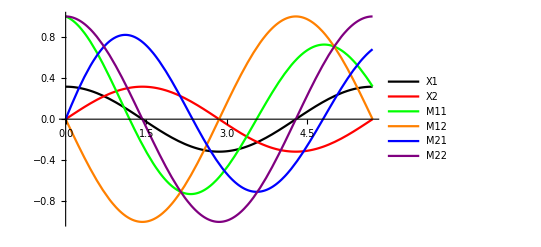

```mathematica
Plot[{X1[t]/. sol, X2[t]/. sol,M11[t]/. sol, M12[t]/. sol,M21[t]/. sol,M22[t]/. sol},{t,0,periodT}, PlotLegends->{"X1", "X2", "M11", "M12", "M21","M22"},PlotStyle->{Black, Red, Green, Orange, Blue,Purple}]
```

### e)

```mathematica
(*Taking out the different M:s and then put them into matrix for a better representation/visualizing*)
M11 = M11[periodT]/.sol[[1]];
M12  = M12[periodT]/.sol[[1]];
M21 = M21[periodT]/.sol[[1]];
M22 = M22[periodT]/.sol[[1]];
Mmatrix = {{M11, M12},{M21, M22}};
Mmatrix//MatrixForm
```

(0.319053 | 2.12317×10^-8
0.680947 | 1.)

### f)

```mathematica
stabilityExpSOfSep = Log[Eigenvalues[Mmatrix]]/periodT
```

{5.78753×10^-9,-0.2}

```mathematica
(*sigma1<=sigma2 therefore sigma1 is the second term in the above vector and sigma2 the first term*)
sigma1 = stabilityExpSOfSep[[2]]
sigam2  = stabilityExpSOfSep[[1]]
```

-0.2

5.78753×10^-9